-2.

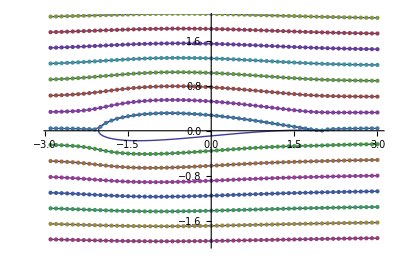

```mathematica
(*Ben Robinson Math 786 Joukowski Airfoil and Streams*)
Clear[z,d,x,y,j,i,Δj, Δx,Δy,n,w,u,Δz,s,lPlot,pList, k,yy]

Δx=-0.1;
Δy = .05;
d=((Δx-1)^2+(Δy-0)^2)^(1/2);
ρ[t_]:=(d*Cos[t]+Δx)+ⅈ*(d*Sin[t]+Δy);
f[z_]:=z + 1/z;
γ[t_]:=f[ρ[t]];
Δz=Δx+ⅈ*Δy;
airfoil = ParametricPlot[{Re[γ[t]],Im[γ[t]]},{t,0,2π}];
k=0;
yy=-2.
Δyy=.25;
bigList={};
bezList={};
(*Outer loop*)
While[yy≤2.,
Δj=.1;
Subscript[j, i-1]=-3.;
Subscript[pList, k]={};
(*Inner loop*)
While[Subscript[j, i-1]<3.,
	(*Print[Sign[Subscript[j, i]]];*)
	Subscript[j, i]=Subscript[j, i-1]+Δj;
	F[z_]:=(z+(Sign[Subscript[j, i]]*(z^2-4)^(1/2))-2*Δz)/(2*d)+(2*d)/(z+(Sign[Subscript[j, i]]*(z^2-4)^(1/2))-2*Δz);
	s = FindRoot[Im[F[Subscript[j, i]+(ⅈ*u)]]==yy,{u,2.}][[1]][[2]];
	AppendTo[Subscript[pList, k],{Subscript[j, i],s}]; 
	Subscript[j, i-1]=Subscript[j, i]
	];
AppendTo[bigList,Subscript[pList, k]];
Subscript[bez, k]=BSplineFunction[Subscript[pList, k]];
Subscript[plot, k]=ParametricPlot[Subscript[bez, k][t],{t,0,1}];
AppendTo[bezList,Subscript[plot, k]];
yy=yy+Δyy;
	k++
]
lPlot=ListPlot[bigList];

Show[ airfoil,bezList,lPlot, PlotRange->{-2,2}]
```